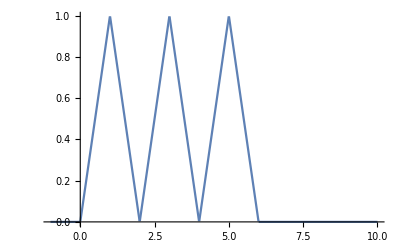

```mathematica
r[x_] := HeavisideTheta[x]*x
Plot[r[x] - 2r[x-1] + 2r[x-2] - 2r[x-3] + 2r[x-4] - 2r[x-5] + r[x-6], {x, -1, 10}]
```

```mathematica
Manipulate[Plot[1/(2a)(1 - Cos[a*π*x]) + (1 - a)x, {x, -1, 10}, PlotRange->{-15, 15}], {a, 0, 1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
-1/2 Log[2*π*n*(1/2 + y)*(1/2 - y)] + n*(-1/2 - y)Log[1/2 + y] + n*(-1/2 + y)Log[1/2 - y]
(*Plot[% /. n->1, {y, -.5, .5}]*)
Series[%, {y, 0, 4}]
```

n (-1/2+y) Log[1/2-y]+n (-1/2-y) Log[1/2+y]-1/2 Log[2 n π (1/2-y) (1/2+y)]

(n Log[2]+1/2 (Log[2]-Log[n]-Log[π]))+(2-2 n) y^2+(4-(4 n)/3) y^4+O[y]^5

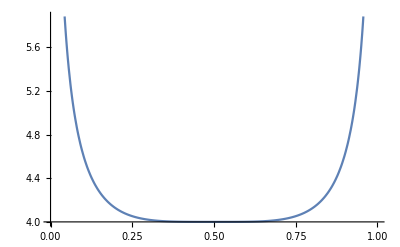

```mathematica
Plot[1/(Sqrt[x*(1-x)]*x^x(1-x)^(1-x)), {x, 0, 1}]
```